### Interpolation and Fit Exercise 1. A data set is in a file https://www.physics.uci.edu/~taborek/Exdata.dat Import the data, and use ListPlot to examine it.

```mathematica
data1=Import["https://www.physics.uci.edu/~taborek/Exdata.dat"]
```

{{0.001,-0.0323071},{0.101,-0.950955},{0.201,-0.986505},{0.301,-1.35334},{0.401,-1.56136},{0.501,-1.81819},{0.601,-1.50116},{0.701,-1.41085},{0.801,-1.24734},{0.901,-1.30368},{1.001,-1.00423},{1.101,-0.713662},{1.201,-0.520801},{1.301,-0.272153},{1.401,0.0166584},{1.501,0.326215},{1.601,0.612875},{1.701,0.96343},{1.801,1.41318},{1.901,1.80601},{2.001,2.22857},{2.101,2.67166},{2.201,2.86813},{2.301,3.37391},{2.401,3.80567},{2.501,4.30789},{2.601,5.07284},{2.701,5.21751},{2.801,5.60222},{2.901,6.27372},{3.001,6.67874},{3.101,7.54797},{3.201,7.97111},{3.301,8.83844},{3.401,9.38518},{3.501,9.75871},{3.601,10.3732},{3.701,11.1852},{3.801,11.3331},{3.901,11.8238}}

### 2. Construct an interpolation function and make a plot of it and compare it to the data points.

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

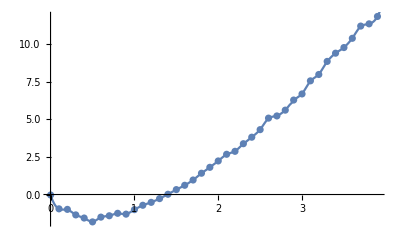

```mathematica
realdataplot= ListPlot[data1];
int1=Interpolation[data1];
guess1=Plot[int1[t],{t,0,4}];
Show[realdataplot,guess1]
```

### 3. You have reason to believe that the data should be describable by a function of the form A x Log[x] + B x . Find the best least squares values for the parameters A and b and make a plot that compares the fit to the data.

```mathematica
form= A x Log[x]+B x;
FindFit[data1,form,{A,B},x]
```

{A→3.03096,B→-1.02558}

```mathematica
fit2 = form /. %
```

-1.02558 x+3.03096 x Log[x]

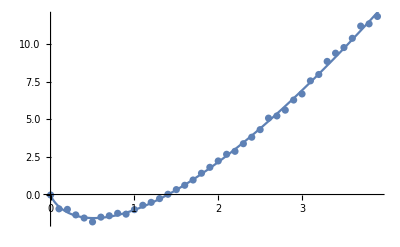

```mathematica
realdataplot= ListPlot[data1];
leastsqplot1=Plot[fit2,{x,0,4}];
Show[realdataplot,leastsqplot1]
```